```mathematica
(*39.1*)
x= RandomInteger[100];
{x, x+1,x+2,x^2}
```

{30,31,32,900}

```mathematica
(*39.2*)
```

```mathematica
x:= RandomInteger[100];
{x, x+1,x+2,x^2}
```

{91,64,21,2916}

```mathematica
(*40.1*)f[n_]:=n^2;
f[3]
```

9

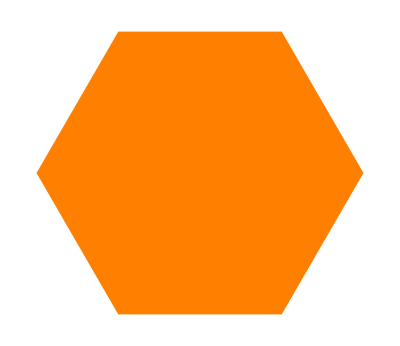

```mathematica
(*40.2*)poly[n_]:=Graphics[Style[RegularPolygon[n],Orange]];
poly[6]
```

```mathematica
(*40.3*)g[a_,b_]:=Reverse[{a,b}];
g[2,3]
```

{3,2}

```mathematica
(*40.4*)h[a_,b_]:=(a b)/(a+b)
h[1,2]
```

2/3

```mathematica
(*40.5*)i[a_,b_]:={a+b, a-b,a/b}
i[2,3]
```

{5,-1,2/3}

```mathematica
(*40.6*)
```

```mathematica
evenOdd[n_]:=If[n==0,Red,If[EvenQ[n]==True, Black,White]]
evenOdd[2]
```

GrayLevel[0]

```mathematica
(*40.7*)j[a_,b_,c_]:=If[a==1,b+c,If[a==2,b c,If[a==3,b^c,Null]]]
j[3,2,3]
```

8

```mathematica
(*40.8*)l[n_]:= {
l[0]=1,
l[1]=1,
l[n-1]+l[n-2]}
l[3]
```

{1,1,{2,2,3}}

```mathematica
(*40.9*)animal[n_String]:=Interpreter[n]["Animal"]["Image"] (*for some reason, even basic uses of entities are not working right now*)
animal["tiger"]
```

Missing[NotAvailable,Image]

```mathematica
(*40.10*) nearWords[word_String,n_]:=(
p=Flatten[Position[WordList[],word]];Nearest[WordList[],word,n])
nearWords["grape",5]
```

{grape,crape,drape,gape,grace}

```mathematica
MapApply[f,expr]
```

```mathematica
MapApply[ToUpperCase,{{"a"}}]
```

{A}

```mathematica
MapApply[evenOdd,{{1},{2},{3}}]
```

{GrayLevel[1],GrayLevel[0],GrayLevel[1]}